```mathematica
pUnrep :=1200;
Kd:=800;
n:=2;
tauR:=120;
tauP:=3600;
gr:=Log[2]/tauR;
gp:=Log[2]/tauP;
b:=10;
kp:=b*gr;
krmax:=pUnrep*gr*gp/kp;
```

```mathematica
kr[p_,n_,Kd_]:=krmax/(1+(p/Kd)^n);
Derivkr[p_,n_,Kd_]:=-(krmax n (p/Kd)^(-1+n))/(Kd (1+(p/Kd)^n)^2);
k0[pAve_,n_,Kd_]:=kr[pAve,n,Kd]-pAve*Derivkr[pAve,n,Kd];
k1[pAve_,n_,Kd_]:=-Derivkr[pAve,n,Kd];
pAve[n_,Kd_]:=({p,r}/.NSolve[0==kr[p,n,Kd,krmax]-gr*r&&0==kp*r-gp*p,{p,r},Reals])
which[n_,Kd_]:=Select[pAve[n,Kd],#[[1]]>0&][[1]][[1]]
pAveA[k0_,k1_]:=(1/(1+b*k1/gp))*(k0*b)/gp;
fano[k1_]:=((1-k1/gp)/(1+b*k1/gp))*b/(1+gp/gr)+1;
```

```mathematica
toplotN =Table[{which[n,Kd],fano[k1[which[n,Kd],n,Kd]]},{n,0,20,0.5}];
toplotKd=Table[{which[n,Kd],fano[k1[which[n,Kd],n,Kd]]},{Kd,0,5000,100}];
```

ReplaceAll::reps: {NSolve[0 == kr[p, 0., 800, 1/30\ Log[« 1 »]] - 1/120\ r\ Log[2] && 0 == -p\ Log[2]/3600 + 1/12\ r\ Log[2], {p, r}, Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of ReplaceAll[] does not exist.

ReplaceAll::reps: {NSolve[0 == kr[p, 0., 800, 1/30\ Log[« 1 »]] - 1/120\ r\ Log[2] && 0 == -p\ Log[2]/3600 + 1/12\ r\ Log[2], {p, r}, Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of ReplaceAll[] does not exist.

ReplaceAll::reps: {NSolve[0 == kr[p, 0.5, 800, 1/30\ Log[« 1 »]] - 1/120\ r\ Log[2] && 0 == -p\ Log[2]/3600 + 1/12\ r\ Log[2], {p, r}, Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll :: argt will be suppressed during this calculation.

Part::partw: Part 1 of ReplaceAll[] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[0 == kr[p, 2, 0, 1/30\ Log[« 1 »]] - 1/120\ r\ Log[2] && 0 == -p\ Log[2]/3600 + 1/12\ r\ Log[2], {p, r}, Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of ReplaceAll[] does not exist.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[0 == kr[p, 2, 0, 1/30\ Log[« 1 »]] - 1/120\ r\ Log[2] && 0 == -p\ Log[2]/3600 + 1/12\ r\ Log[2], {p, r}, Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of ReplaceAll[] does not exist.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

General::stop: Further output of NSolve :: nsmet will be suppressed during this calculation.

ReplaceAll::reps: {NSolve[0 == kr[p, 2, 100, 1/30\ Log[« 1 »]] - 1/120\ r\ Log[2] && 0 == -p\ Log[2]/3600 + 1/12\ r\ Log[2], {p, r}, Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll :: argt will be suppressed during this calculation.

Part::partw: Part 1 of ReplaceAll[] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
p2=ListPlot[{toplotN,toplotKd},Joined->True];
```

```mathematica
NN=Import["/home/gutiloluis/61Monograph/gillespie/n.dat"];
KD=Import["/home/gutiloluis/61Monograph/gillespie/Kd.dat"];
```

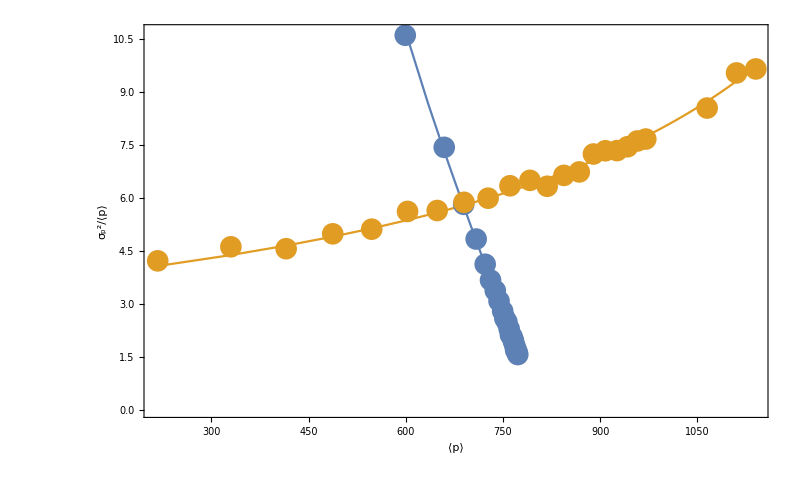

```mathematica
p3=ListPlot[{NN,KD},PlotRange->{0,12}PlotLegends->Placed[LineLegend[{"b","k_r","τ_p"},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",35},LegendLayout->{"Row",3},Spacings->0.2],{0.88,0.2}]];
Show[{p2,p3},ImageSize->800,Frame->True,FrameStyle->Black,FrameLabel->{Text[Style[ToExpression["\\langle p\\rangle",TeXForm,HoldForm],Large]],Text[Style[ToExpression["\\frac{\\sigma_p^2}{\\langle p\\rangle}",TeXForm,HoldForm],30]]},RotateLabel->False,LabelStyle->Directive[18,FontFamily->"Palatino Linotype",Black]]
```